# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψmf,ψexact,ψinitmf,ψinitexact}=CreateQuregs[5,4];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];

(* mean field grounstate (product state) *)
ApplyCircuit[InitZeroState@ψinitmf,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
```

This part (roughly)shows that in the case of exact ground state, the propagators preserves states with hamming weight 1

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=List/@eigvec[[First@Ordering[eigval,1]]];
```

Low g(t)

```mathematica
hbcs0mat=CalcPauliStringMatrix[HBCS[5,ϵ,0]]//Chop;
hbcs0mat9=MatrixExp[-ⅈ *0.5*hbcs0mat  ]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs0mat9,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
(*hamming-weight preserving blocks*)
Table[Length@block->{BaseForm[#,2]&/@block},{block,blocks}]//Column
```

10→{{111_2,1011_2,1101_2,1110_2,10011_2,10101_2,10110_2,11001_2,11010_2,11100_2}}
10→{{11_2,101_2,110_2,1001_2,1010_2,1100_2,10001_2,10010_2,10100_2,11000_2}}
5→{{1111_2,10111_2,11011_2,11101_2,11110_2}}
5→{{1_2,10_2,100_2,1000_2,10000_2}}
1→{{11111_2}}
1→{{0_2}}

```mathematica
CloneQureg[ψmf,ψinitmf];
CloneQureg[ψexact,ψinitexact];
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
```

```mathematica
(* mean-field approximate ground state is bad, and it's all over the place*)
vmf=Chop@GetQuregMatrix@ψmf;
Table[If[vmf[[j]]!=0,{BaseForm[j-1,2],1},{BaseForm[j-1,2],0}],{j,Length@vmf}]
```

{{0_2,1},{1_2,1},{10_2,1},{11_2,1},{100_2,1},{101_2,1},{110_2,1},{111_2,1},{1000_2,1},{1001_2,1},{1010_2,1},{1011_2,1},{1100_2,1},{1101_2,1},{1110_2,1},{1111_2,1},{10000_2,1},{10001_2,1},{10010_2,1},{10011_2,1},{10100_2,1},{10101_2,1},{10110_2,1},{10111_2,1},{11000_2,1},{11001_2,1},{11010_2,1},{11011_2,1},{11100_2,1},{11101_2,1},{11110_2,1},{11111_2,1}}

```mathematica
(* The exact ground state preserves hamming weight 1*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

High g(t)

```mathematica
hbcs10=HBCS[5,ϵ,10];
hbcs10mat=CalcPauliStringMatrix[hbcs10]//Chop;
hbcs10mat05=MatrixExp[-ⅈ hbcs10mat 0.5]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs10mat05,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
```

```mathematica
(* Still preserving the ones at high and low g(t)*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

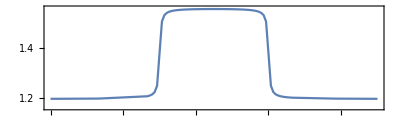

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

**** Compile @Thu 15 Dec 2022 19:11:06 τ=0; δ4. ****

Cycle 1@Thu 15 Dec 2022 19:17:57 completed with ngates=42, cost=2.947008026499276e-6, at eval=1715

Cycle 2@Thu 15 Dec 2022 19:20:21 adjust hyperparams, slowdown:True

Cycle 3@Thu 15 Dec 2022 19:34:23 completed with ngates=51, cost=4.4332561233151324e-7, at eval=4327

Cycle 4@Thu 15 Dec 2022 19:52:53 completed with ngates=62, cost=2.4772069950884656e-8, at eval=6616

Cycle 5@Thu 15 Dec 2022 20:00:19 adjust hyperparams, slowdown:True

Cycle 6@Thu 15 Dec 2022 20:16:55 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 20:20:57 adjust hyperparams, slowdown:False

Cycle 8@Thu 15 Dec 2022 20:25:18 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.47721×10^-8

τ=4.; δ=4.; cost=2.47721×10^-8; ngates=62; runtime=97.6628 min

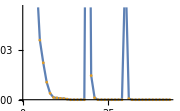

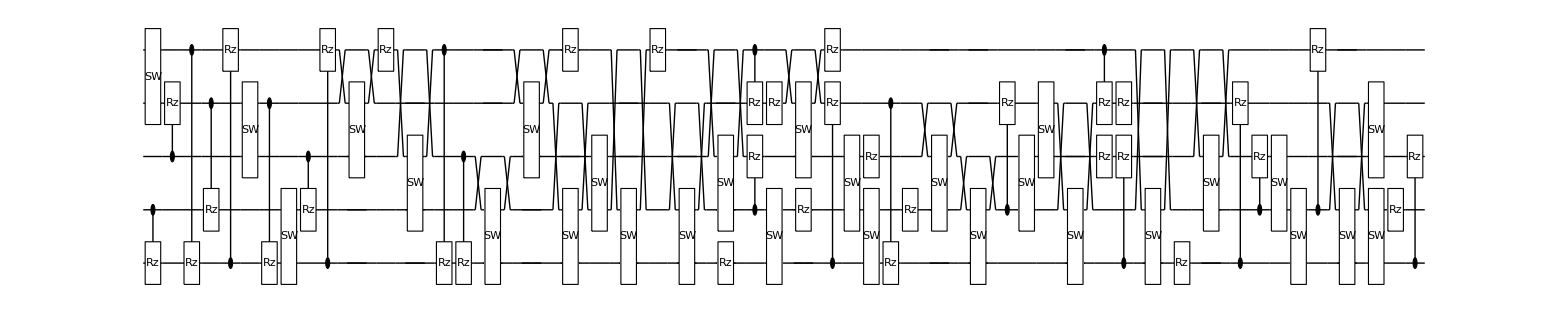

**** Compile @Thu 15 Dec 2022 20:48:46 τ=4.; δ4. ****

Cycle 1@Thu 15 Dec 2022 20:54:34 completed with ngates=35, cost=8.705446470802514e-6, at eval=1706

Cycle 2@Thu 15 Dec 2022 20:56:23 adjust hyperparams, slowdown:True

Cycle 3@Thu 15 Dec 2022 21:05:39 completed with ngates=53, cost=1.1588684541985472e-6, at eval=3858

Cycle 4@Thu 15 Dec 2022 21:22:03 completed with ngates=72, cost=1.5445222578680529e-7, at eval=5784

Cycle 5@Thu 15 Dec 2022 21:48:48 completed with ngates=94, cost=1.8000301582610234e-8, at eval=7964

Cycle 6@Thu 15 Dec 2022 22:00:13 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 22:24:12 adjust hyperparams, slowdown:True

Cycle 8@Thu 15 Dec 2022 22:30:42 adjust hyperparams, slowdown:False

Cycle 9@Thu 15 Dec 2022 22:37:40 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.80003×10^-8

τ=8.; δ=4.; cost=1.80003×10^-8; ngates=94; runtime=117.49 min

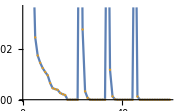

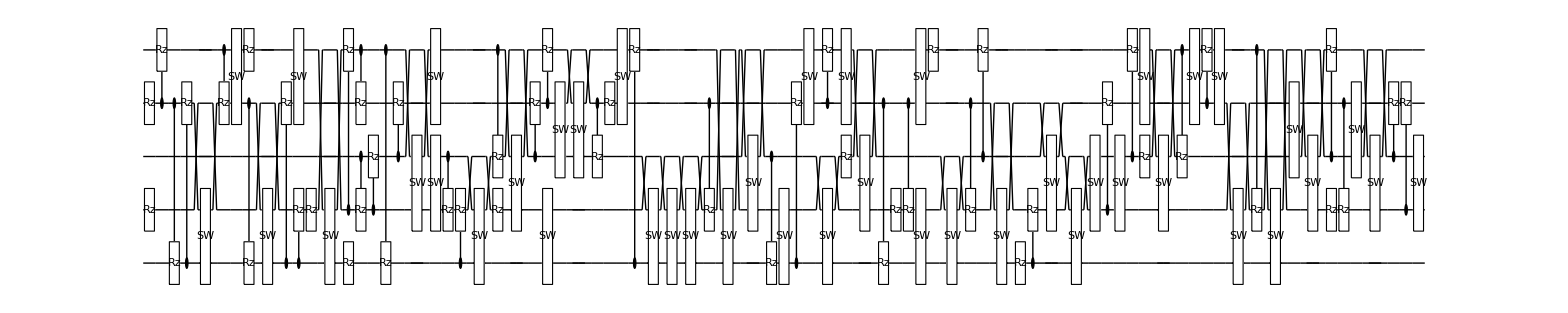

**** Compile @Thu 15 Dec 2022 22:46:22 τ=8.; δ0.2 ****

Cycle 1@Thu 15 Dec 2022 22:51:35 completed with ngates=31, cost=0.0003538152047738441, at eval=1732

Cycle 2@Thu 15 Dec 2022 22:54:33 completed with ngates=34, cost=0.000013242712452621319, at eval=2935

Cycle 3@Thu 15 Dec 2022 22:56:22 adjust hyperparams, slowdown:True

Cycle 4@Thu 15 Dec 2022 23:05:11 completed with ngates=43, cost=5.893423828950972e-7, at eval=5357

Cycle 5@Thu 15 Dec 2022 23:15:54 completed with ngates=60, cost=9.192599625951203e-8, at eval=7018

Cycle 6@Thu 15 Dec 2022 23:22:48 adjust hyperparams, slowdown:True

Cycle 7@Thu 15 Dec 2022 23:38:11 adjust hyperparams, slowdown:True

Cycle 8@Thu 15 Dec 2022 23:41:39 adjust hyperparams, slowdown:False

Cycle 9@Thu 15 Dec 2022 23:45:21 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.1926×10^-8

τ=8.2; δ=0.2; cost=9.1926×10^-8; ngates=60; runtime=61.8066 min

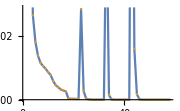

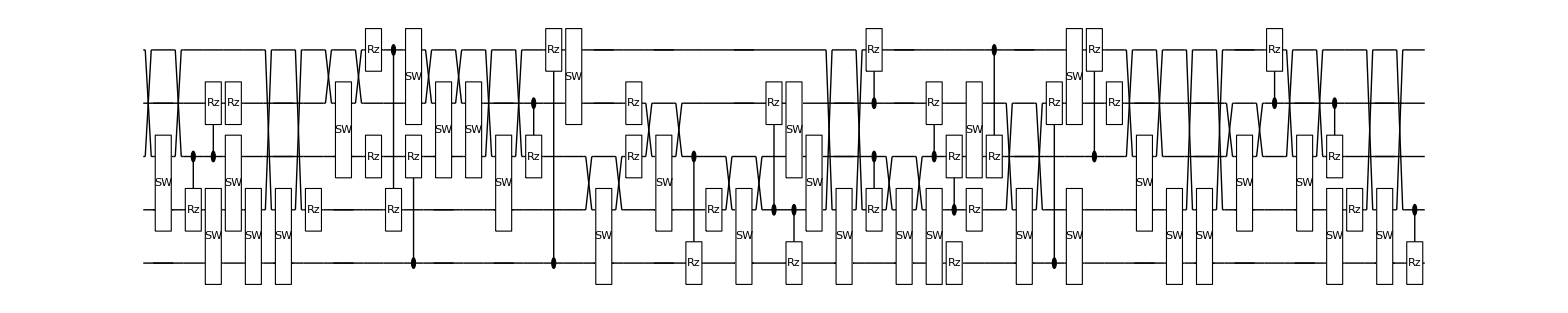

**** Compile @Thu 15 Dec 2022 23:48:16 τ=8.2; δ0.2 ****

Cycle 1@Thu 15 Dec 2022 23:53:57 completed with ngates=34, cost=0.000033447434527822395, at eval=1684

Cycle 2@Thu 15 Dec 2022 23:59:28 completed with ngates=39, cost=1.9002964379843945e-6, at eval=3450

Cycle 3@Fri 16 Dec 2022 00:01:36 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 00:12:27 completed with ngates=63, cost=9.754805985195958e-8, at eval=5537

Cycle 5@Fri 16 Dec 2022 00:19:26 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: Invalid arguments. See ?ApplyCircuitDerivs

General::stop: Further output of ApplyCircuitDerivs::error will be suppressed during this calculation.

Cycle 6@Fri 16 Dec 2022 00:35:37 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 00:39:26 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 00:43:19 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=9.75481×10^-8

τ=8.4; δ=0.2; cost=9.75481×10^-8; ngates=63; runtime=57.997 min

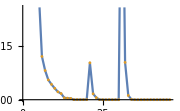

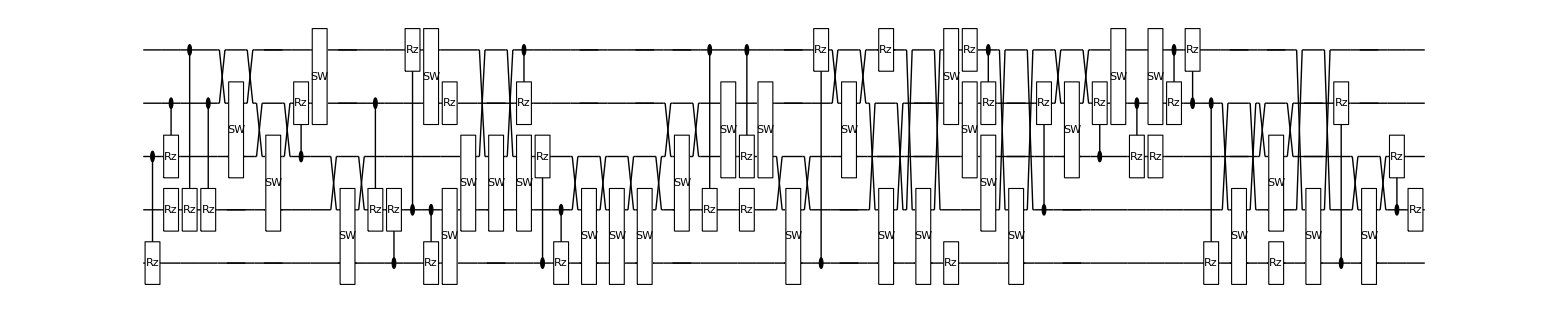

**** Compile @Fri 16 Dec 2022 00:46:22 τ=8.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 00:53:14 completed with ngates=51, cost=2.64562463236917e-6, at eval=1607

Cycle 2@Fri 16 Dec 2022 00:56:11 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 01:01:52 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 01:15:31 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 01:18:30 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.64562×10^-6

τ=8.6; δ=0.2; cost=2.12289×10^-6; ngates=51; runtime=33.7408 min

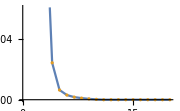

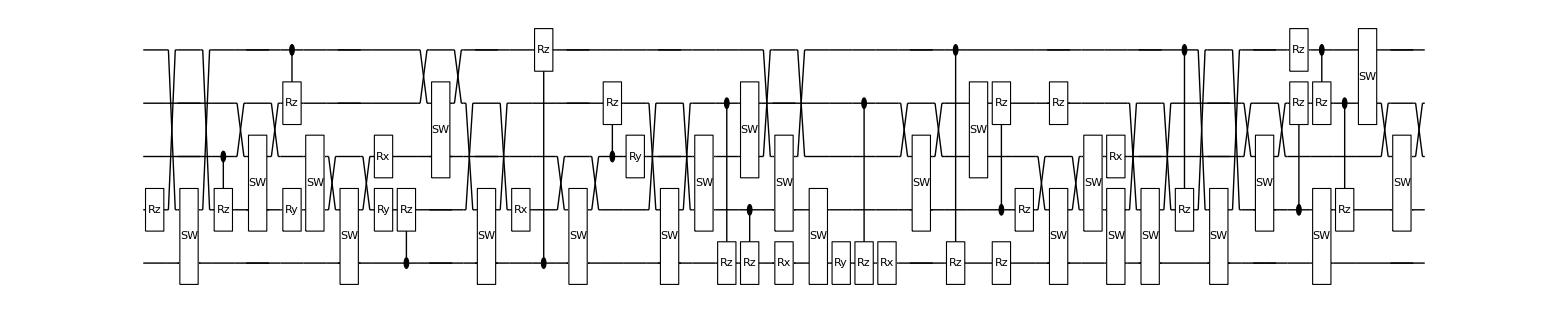

**** Compile @Fri 16 Dec 2022 01:20:13 τ=8.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 01:25:30 completed with ngates=42, cost=0.0001378761373466153, at eval=1477

Cycle 2@Fri 16 Dec 2022 01:29:35 completed with ngates=33, cost=0.000026819736095529123, at eval=2840

Cycle 3@Fri 16 Dec 2022 01:31:10 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 01:38:41 completed with ngates=39, cost=3.404436585863202e-6, at eval=5041

Cycle 5@Fri 16 Dec 2022 01:48:50 completed with ngates=60, cost=2.8256308959306864e-7, at eval=6696

Cycle 6@Fri 16 Dec 2022 01:55:31 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 02:11:23 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 02:27:24 completed with ngates=69, cost=4.756276372752666e-8, at eval=10256

Cycle 9@Fri 16 Dec 2022 02:43:20 completed with ngates=81, cost=2.754279593286668e-8, at eval=12020

Cycle 10@Fri 16 Dec 2022 03:06:04 completed with ngates=95, cost=1.9031677456204932e-8, at eval=14003

Cycle 11@Fri 16 Dec 2022 03:12:34 adjust hyperparams, slowdown:False

Cycle 12@Fri 16 Dec 2022 03:19:18 adjust hyperparams, slowdown:False

Cycle 13@Fri 16 Dec 2022 03:26:38 adjust hyperparams, slowdown:False

Cycle 14@Fri 16 Dec 2022 03:55:21 completed with ngates=101, cost=9.631666686438223e-9, at eval=17600

@cycle15, pathetic result.

Cycle 15@Fri 16 Dec 2022 04:03:54 adjust hyperparams, slowdown:False

Cycle 16@Fri 16 Dec 2022 04:36:37 completed with ngates=104, cost=4.0873575635203e-9, at eval=20438

Cycle 17@Fri 16 Dec 2022 05:14:38 completed with ngates=111, cost=2.6679100040283288e-9, at eval=22833

Cycle 18@Fri 16 Dec 2022 05:57:17 completed with ngates=116, cost=4.4996739667624297e-10, at eval=25306

τ=8.8; δ=0.2; cost=4.49967×10^-10; ngates=116; runtime=292.862 min

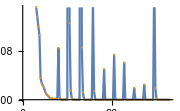

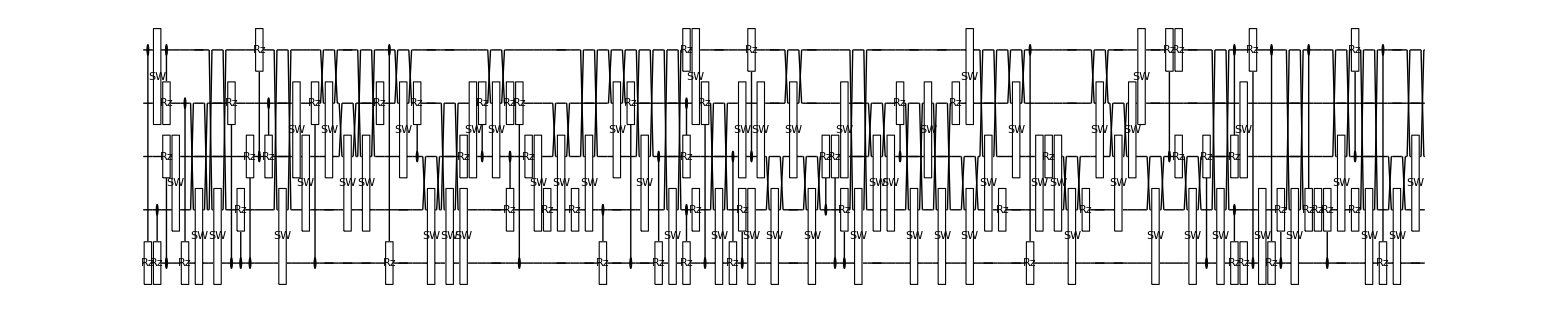

**** Compile @Fri 16 Dec 2022 06:13:11 τ=8.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 06:19:04 completed with ngates=40, cost=8.967378830604389e-7, at eval=1682

Cycle 2@Fri 16 Dec 2022 06:21:12 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 06:25:38 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 06:36:46 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 06:38:50 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.96738×10^-7

τ=9.; δ=0.2; cost=7.39663×10^-7; ngates=40; runtime=26.5438 min

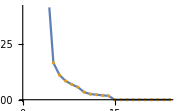

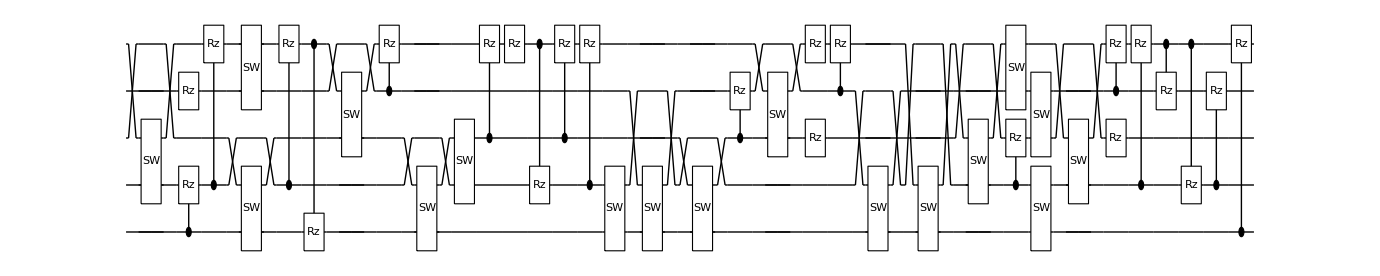

**** Compile @Fri 16 Dec 2022 06:39:49 τ=9.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 06:45:39 completed with ngates=42, cost=3.7689723451084234e-6, at eval=1528

Cycle 2@Fri 16 Dec 2022 06:47:55 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 06:58:30 completed with ngates=57, cost=1.6273640546238255e-7, at eval=3599

Cycle 4@Fri 16 Dec 2022 07:05:15 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 07:20:10 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 07:23:27 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 07:26:54 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.62736×10^-7

τ=9.2; δ=0.2; cost=1.62736×10^-7; ngates=57; runtime=49.4399 min

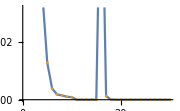

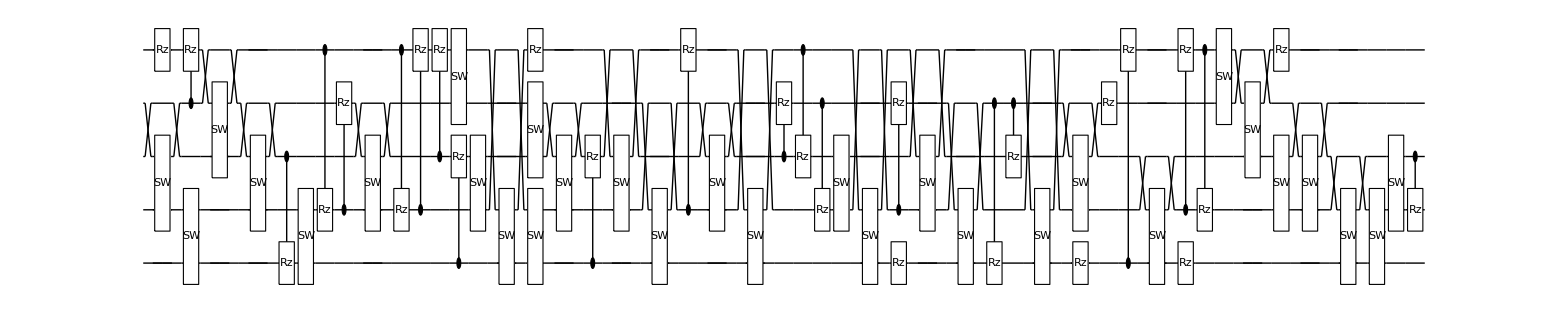

**** Compile @Fri 16 Dec 2022 07:29:22 τ=9.2; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 07:37:00 completed with ngates=40, cost=5.232589668224819e-7, at eval=2202

Cycle 2@Fri 16 Dec 2022 07:39:13 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 07:51:17 completed with ngates=64, cost=2.979185897977743e-9, at eval=4295

Cycle 4@Fri 16 Dec 2022 07:58:54 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 08:16:09 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 08:20:13 adjust hyperparams, slowdown:False

Cycle 7@Fri 16 Dec 2022 08:24:22 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=2.97919×10^-9

τ=9.4; δ=0.2; cost=2.97919×10^-9; ngates=64; runtime=58.4111 min

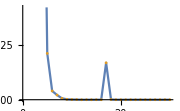

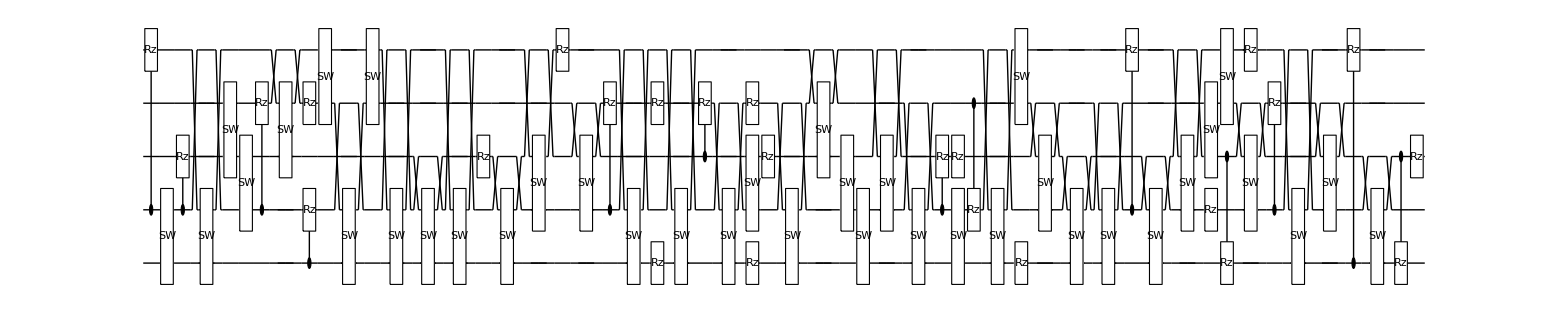

**** Compile @Fri 16 Dec 2022 08:27:53 τ=9.4; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 08:35:50 completed with ngates=50, cost=8.654403237384756e-7, at eval=1871

Cycle 2@Fri 16 Dec 2022 08:38:33 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 08:44:00 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 08:57:12 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 09:00:02 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=8.6544×10^-7

τ=9.6; δ=0.2; cost=8.6544×10^-7; ngates=50; runtime=34.1201 min

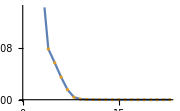

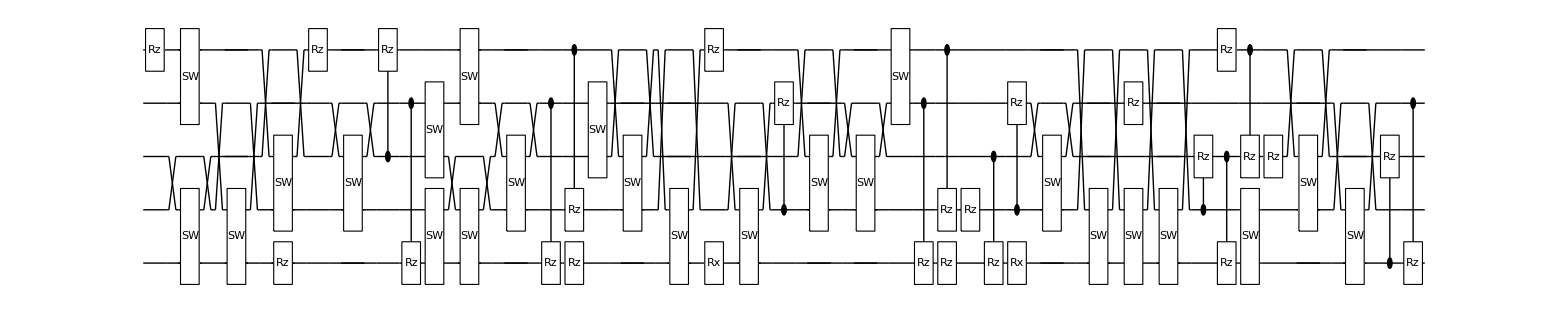

**** Compile @Fri 16 Dec 2022 09:02:06 τ=9.6; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 09:08:01 completed with ngates=37, cost=1.1446651030366795e-6, at eval=1510

Cycle 2@Fri 16 Dec 2022 09:14:24 completed with ngates=52, cost=6.144624474790916e-7, at eval=2913

Cycle 3@Fri 16 Dec 2022 09:24:00 completed with ngates=65, cost=5.796246438372066e-8, at eval=4455

Cycle 4@Fri 16 Dec 2022 09:27:41 adjust hyperparams, slowdown:True

Cycle 5@Fri 16 Dec 2022 09:34:59 adjust hyperparams, slowdown:True

Cycle 6@Fri 16 Dec 2022 09:51:51 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 09:55:38 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.79625×10^-8

τ=9.8; δ=0.2; cost=5.79625×10^-8; ngates=65; runtime=56.8412 min

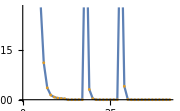

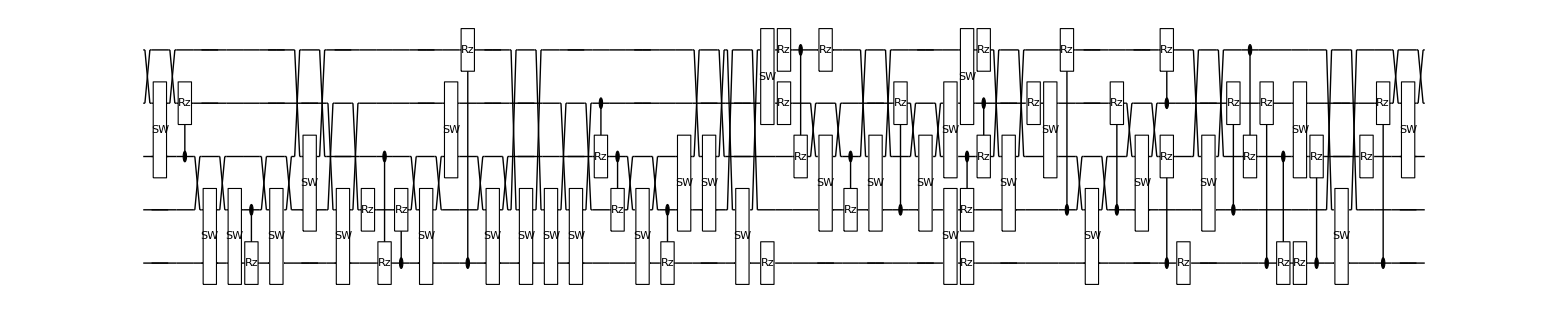

**** Compile @Fri 16 Dec 2022 09:59:03 τ=9.8; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 10:04:21 completed with ngates=32, cost=0.00003090614438772121, at eval=1680

Cycle 2@Fri 16 Dec 2022 10:08:55 completed with ngates=38, cost=5.547322535992549e-6, at eval=3191

Cycle 3@Fri 16 Dec 2022 10:14:52 completed with ngates=50, cost=1.1755858260187324e-6, at eval=4711

Cycle 4@Fri 16 Dec 2022 10:23:47 completed with ngates=63, cost=2.2559985934922366e-7, at eval=6289

Cycle 5@Fri 16 Dec 2022 10:37:58 completed with ngates=79, cost=5.721933216129571e-8, at eval=8068

Cycle 6@Fri 16 Dec 2022 10:42:34 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 10:51:04 adjust hyperparams, slowdown:True

Cycle 8@Fri 16 Dec 2022 11:11:58 adjust hyperparams, slowdown:True

Cycle 9@Fri 16 Dec 2022 11:17:33 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=5.72193×10^-8

τ=10.; δ=0.2; cost=5.72193×10^-8; ngates=79; runtime=86.7073 min

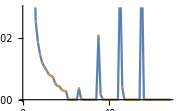

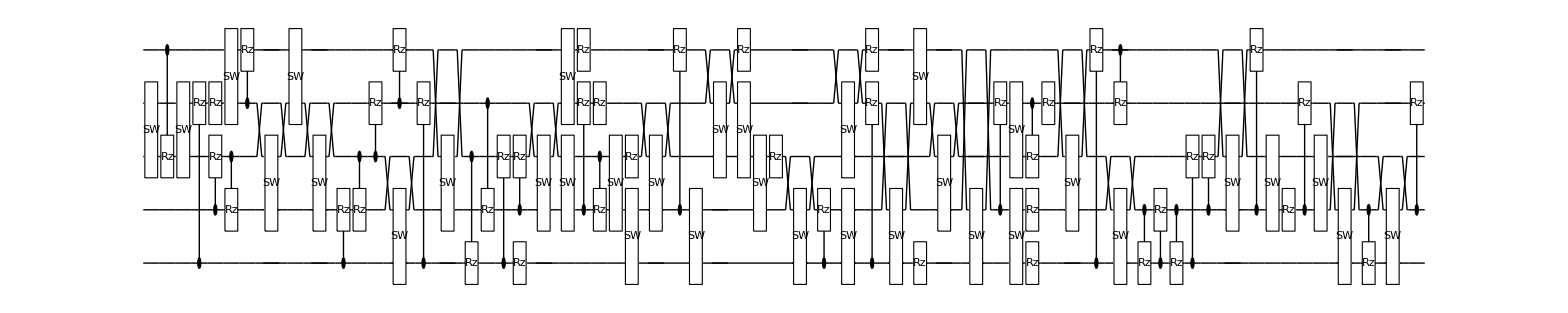

**** Compile @Fri 16 Dec 2022 11:25:51 τ=10.; δ0.2 ****

Cycle 1@Fri 16 Dec 2022 11:32:35 completed with ngates=41, cost=1.5208053063542337e-6, at eval=1697

Cycle 2@Fri 16 Dec 2022 11:35:05 adjust hyperparams, slowdown:True

Cycle 3@Fri 16 Dec 2022 11:40:13 adjust hyperparams, slowdown:True

Cycle 4@Fri 16 Dec 2022 12:05:54 completed with ngates=51, cost=2.5002078785085757e-7, at eval=5623

Cycle 5@Fri 16 Dec 2022 12:51:38 completed with ngates=85, cost=1.0096556590788452e-8, at eval=8643

Cycle 6@Fri 16 Dec 2022 13:16:01 adjust hyperparams, slowdown:True

Cycle 7@Fri 16 Dec 2022 13:23:03 adjust hyperparams, slowdown:False

Cycle 8@Fri 16 Dec 2022 13:30:19 adjust hyperparams, slowdown:False

@cycle9, pathetic result.

Cycle 9@Fri 16 Dec 2022 13:38:08 adjust hyperparams, slowdown:False

pruning exceeds the maxcost: 1.×10^-9; cost=1.00966×10^-8

τ=10.2; δ=0.2; cost=1.00966×10^-8; ngates=85; runtime=177.807 min

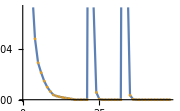

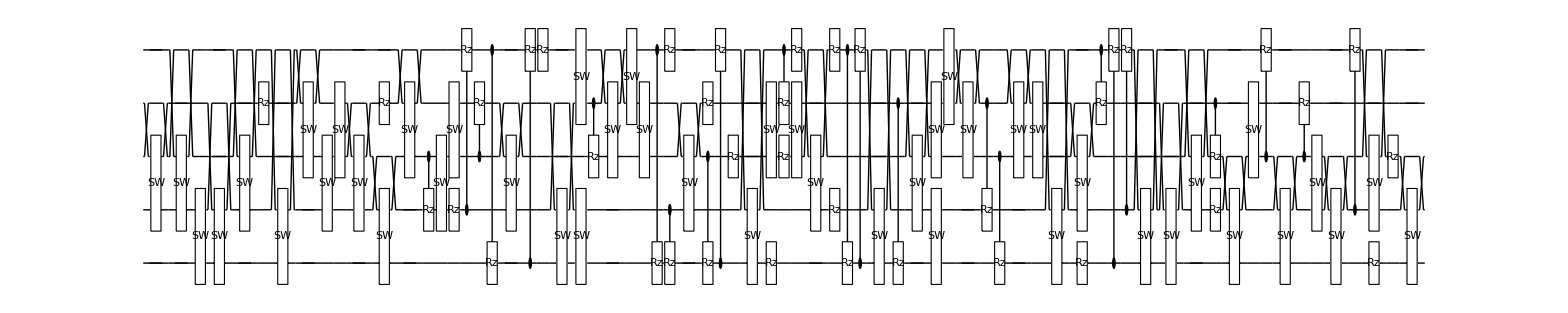

**** Compile @Fri 16 Dec 2022 14:23:41 τ=10.2; δ0.2 ****

```mathematica
τ=0;
bcscompile={};
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
τ+=δ;
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
AppendTo[bcscompile,{τ,δ,res}];

DumpSave["bcscompile.mx",bcscompile];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz,5];
,{δ,δτ[[2;;]]}];
```

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
4/0.01
```

400.

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[ApplyCircuit[ψexact,res[[4]]/.res[[5]]],{400}];
```

```mathematica
AppendTo[rexactcomp,{4.,CalcFidelity[ψexact,ψinitexact]}]
```

{{0,1},{4.,0.571056}}

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,n,res}=comp;
If[Length@res[[4]]>0,
Table[
ApplyCircuit[ψexact,res[[4]]/.res[[5]]]
,{n}]
];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bcscompile}];
```

```mathematica
rexactcomp
```

{{0,1},{4,0.945221},{8,0.931557},{8.,0.931557},{8.2,0.869006},{8.4,0.349307}}

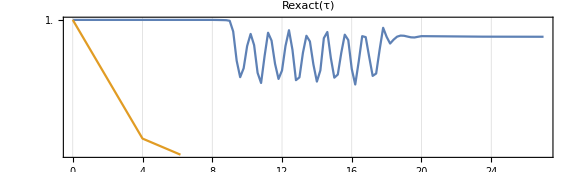

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```